### Scratch

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1},{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]
```

So I need to do a random perturbation at each step, then if the thing is still “alive” say within the range 80 and 120, then we keep going and we just count the number of steps it takes until the pattern goes out of range. So maybe don’t do at each step but just do a random perturbation anywhere.

```mathematica
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ {{"[◼]", "allperts"}}[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

```mathematica
NestWhile[Function[{perts}, 
ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {200, {-100, 100}}], ]
```

```mathematica
Function[perts, Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},If[80<{{"[◼]", "TestCALifeTime"}}[#]<120,  ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec,Join[perts, RandomChoice[{{"[◼]", "allperts"}}[ru, init, txspec, perts]]]]]]
```

```mathematica
ParallelTable[
SeedRandom[111222+i];
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},
NestWhile[
Join[#, RandomChoice[{{"[◼]", "allperts"}}[First[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]]]]&,<||>,
60<
{{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]<140&, 1, 10]], {i, 100}]
```

{<|{73,115}→3,{76,116}→2,{54,114}→1,{94,105}→3|>,<|{49,127}→1,{73,120}→3,{117,136}→1,{3,112}→2|>,<|{19,115}→3|>,<|{76,117}→3,{34,118}→0|>,<|{39,117}→3,{63,125}→1,{57,122}→0,{14,113}→2,{94,128}→3,{99,129}→3,{96,120}→3,{110,121}→0,{99,132}→2,{90,130}→3|>,<|{11,111}→3|>,<|{36,121}→2|>,<|{69,110}→3,{32,115}→1,{85,137}→3|>,<|{79,117}→0,{50,115}→2,{80,122}→1,{94,121}→1,{71,131}→0,{54,118}→0,{69,120}→1,{16,115}→1,{32,118}→3|>,<|{39,125}→3,{43,122}→2,{111,114}→2,{47,124}→2,{96,115}→3,{70,109}→3|>,<|{23,115}→3|>,<|{85,128}→2,{7,113}→3,{42,107}→3,{19,118}→0|>,<|{24,110}→2|>,<|{95,110}→3,{89,112}→3,{71,115}→3,{74,130}→1|>,<|{87,128}→3|>,<|{67,123}→3,{67,120}→3,{56,119}→0|>,<|{60,123}→1|>,<|{82,116}→0,{80,120}→3,{68,126}→1,{80,113}→0,{69,119}→0,{54,125}→2,{75,120}→0,{103,118}→1,{74,112}→3,{92,124}→3|>,<|{57,129}→3|>,<|{25,112}→0|>,<|{10,111}→1|>,<|{69,128}→3,{66,115}→3|>,<|{9,113}→0|>,<|{81,127}→2,{61,110}→1|>,<|{84,110}→1,{70,127}→3,{10,111}→3|>,<|{5,112}→1,{83,125}→3|>,<|{41,112}→1,{87,103}→3,{74,104}→0,{84,102}→1,{26,110}→3,{34,108}→0|>,<|{95,108}→3|>,<|{28,117}→3|>,<|{89,128}→2,{63,118}→0,{89,122}→3|>,<|{87,124}→1|>,<|{51,119}→2,{22,115}→2,{57,123}→1,{16,109}→1|>,<|{96,107}→0,{48,123}→2,{59,118}→2,{69,117}→2,{55,123}→0|>,<|{84,130}→2,{73,132}→3,{88,110}→3,{83,112}→3,{115,120}→3|>,<|{69,116}→1|>,<|{49,127}→0,{38,117}→1,{29,114}→3,{19,111}→2|>,<|{88,113}→0,{53,116}→0|>,<|{86,122}→3,{42,117}→0,{61,126}→0|>,<|{86,107}→1,{74,129}→1|>,<|{86,116}→3,{89,117}→2,{26,119}→2,{25,107}→3,{87,128}→1,{76,108}→0,{37,119}→0|>,<|{93,107}→3,{39,125}→1,{25,110}→0|>,<|{12,113}→0|>,<|{27,112}→0|>,<|{40,115}→2,{18,110}→1,{88,132}→0,{68,125}→0,{83,130}→2|>,<|{69,119}→3|>,<|{49,114}→0,{99,120}→0,{66,128}→3,{30,113}→3|>,<|{14,114}→2|>,<|{73,116}→0,{81,110}→1,{2,113}→1|>,<|{38,117}→3,{38,112}→0,{42,120}→3|>,<|{51,126}→3|>,<|{75,118}→0,{87,109}→0,{70,119}→0,{61,124}→0,{22,108}→0|>,<|{90,107}→1,{52,112}→1|>,<|{32,120}→2,{19,115}→2,{23,107}→2,{67,109}→3|>,<|{76,118}→3,{66,124}→2|>,<|{73,120}→0,{27,117}→0|>,<|{56,123}→1,{66,130}→0,{63,117}→0|>,<|{57,126}→0,{80,107}→3,{35,113}→0|>,<|{72,121}→3,{103,115}→3|>,<|{79,115}→1,{66,120}→3,{93,126}→3|>,<|{48,123}→3,{51,118}→3,{59,108}→2|>,<|{92,112}→3,{51,113}→0|>,<|{75,116}→0,{57,129}→1,{71,124}→1|>,<|{75,115}→1,{83,110}→0,{69,119}→3|>,<|{40,111}→0,{14,116}→2,{95,111}→0,{83,112}→0,{88,119}→0,{68,115}→1,{95,115}→1,{112,131}→3,{62,113}→1,{82,121}→0|>,<|{74,132}→0,{7,114}→0,{98,118}→2,{0,111}→0,{0,118}→2,{1,118}→1,{86,134}→3|>,<|{56,121}→3,{132,109}→3|>,<|{59,123}→3,{93,120}→0,{51,123}→0,{82,119}→0,{67,121}→2,{105,131}→0,{109,135}→2,{56,111}→0,{109,124}→3,{113,115}→3|>,<|{73,122}→3|>,<|{15,113}→0|>,<|{55,116}→0|>,<|{37,112}→2,{63,114}→1|>,<|{70,127}→1|>,<|{53,127}→0|>,<|{67,121}→0,{100,113}→3,{37,114}→3|>,<|{66,108}→1,{26,107}→0,{34,119}→0|>,<|{53,114}→2,{25,114}→3|>,<|{70,122}→0,{24,118}→1,{76,127}→0,{34,114}→3,{36,117}→1|>,<|{18,109}→0|>,<|{21,114}→3,{73,107}→3,{95,114}→1,{11,114}→2|>,<|{36,121}→1,{53,119}→0,{23,107}→0|>,<|{55,115}→3|>,<|{90,114}→0,{16,110}→1|>,<|{53,113}→3,{54,127}→1|>,<|{73,131}→1,{66,119}→0,{44,123}→1|>,<|{14,111}→3|>,<|{86,109}→1,{50,121}→3,{34,114}→2,{68,121}→1,{67,118}→1,{108,127}→3|>,<|{79,117}→1,{64,111}→1|>,<|{58,125}→1,{36,118}→0,{93,123}→1,{61,119}→0,{55,120}→1,{115,125}→1|>,<|{78,130}→0|>,<|{53,111}→0|>,<|{12,111}→0,{19,114}→3|>,<|{48,120}→1|>,<|{86,127}→1,{46,118}→2|>,<|{84,116}→1,{91,107}→3|>,<|{72,117}→1,{53,115}→3|>,<|{73,111}→0,{69,127}→0,{87,129}→3|>,<|{87,126}→3|>,<|{41,112}→3|>,<|{68,131}→1,{57,129}→1,{55,116}→2|>,<|{94,108}→0,{64,113}→3|>}

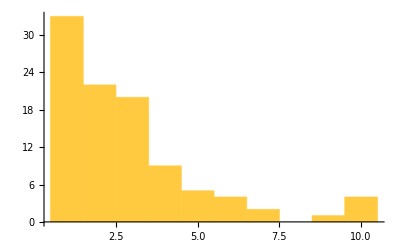

```mathematica
Histogram[Length/@ ]
```

```mathematica
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},RandomChoice[{{"[◼]", "allperts"}}[ru, init, txspec, <||>]]]
```

<|{89,128}→1|>

```mathematica
Join[<||>, <|{89,128}->1|>]
```

<|{89,128}→1|>

```mathematica
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},{{"[◼]", "allperts"}}[ru, init, txspec, Echo@RandomChoice[{{"[◼]", "allperts"}}[ru, init, txspec]]]]
```

<|{46,126}→2|>

SparseArray::list: List expected at position 1 in SparseArray[<|{46,126}→2|>].

Part::partd: Part specification SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

Range::range: Range specification in Range[SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Delete::partw: Part 1 of 0 does not exist.

Delete::pkspec: The expression <|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

Delete::partw: Part 1 of 0 does not exist.

Delete::pkspec: The expression <|{0,2}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,2}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

Delete::partw: Part 1 of 0 does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

Delete::pkspec: The expression <|{0,3}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,3}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

Function::fpct: Too many parameters in {FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$} to be filled from Function[{FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$},FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`vals$14930=Delete[Range[0,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`interpretrule[«1»]⟦2⟧-1],«61»⟦«55»,«55»⟧+1];(Association[«1»]&)/@«63»][2].

Part::pkspec1: The expression SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧ cannot be used as a part specification.

Function::fpct: Too many parameters in {FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$} to be filled from Function[{FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$},FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`vals$14930=Delete[Range[0,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`interpretrule[«1»]⟦2⟧-1],«61»⟦«55»,«55»⟧+1];(Association[«1»]&)/@«63»][2].

```mathematica
{{"[◼]", "allperts"}}[ru, init, txspec]
```

```mathematica
allperts[{299459058088077823758143088095350287424,4,1},{{1}, 0},{200, {-110, 110}}, <|{46,126}->2|>]
```

SparseArray::list: List expected at position 1 in SparseArray[<|{46,126}→2|>].

Part::partd: Part specification SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

Range::range: Range specification in Range[SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Delete::partw: Part 1 of 0 does not exist.

Delete::pkspec: The expression <|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

Delete::partw: Part 1 of 0 does not exist.

Delete::pkspec: The expression <|{0,2}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,2}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

Delete::partw: Part 1 of 0 does not exist.

General::stop: Further output of Delete::partw will be suppressed during this calculation.

Delete::pkspec: The expression <|{0,3}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,3}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«63»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

Function::fpct: Too many parameters in {i$,j$} to be filled from Function[{i$,j$},vals$15163=Delete[Range[0,interpretrule[«1»]⟦2⟧-1],ca$15160⟦i$,j$⟧+1];(Association[{Plus[«2»],j$}→#1]&)/@vals$15163][2].

Part::pkspec1: The expression SparseArray[<|{46,126}→2|>][NonzeroPositions]⟦1,1⟧ cannot be used as a part specification.

Function::fpct: Too many parameters in {i$,j$} to be filled from Function[{i$,j$},vals$15163=Delete[Range[0,interpretrule[«1»]⟦2⟧-1],ca$15160⟦i$,j$⟧+1];(Association[{Plus[«2»],j$}→#1]&)/@vals$15163][2].

```mathematica
ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1}, 0},{200, {-110, 110}}, <|{46,126}->2|>]
```

### Result

```mathematica
eps =  ParallelTable[
SeedRandom[111222+i];
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},
NestWhile[
Join[#, RandomChoice[{{"[◼]", "allperts"}}[First[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]]]]&,<||>,
60<
{{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]<140&, 1]], {i, 1000}];
```

```mathematica
Iconize[eps]
```

```mathematica
eps =;
```

```mathematica
GraphicsRow[Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},
Table[{{"[◼]", "PlotCA"}}[[ru, init, txspec, eps[[1, ;;i]]]], {i,Length[eps[[1]]]}] ]]
```

-Graphics-

```mathematica
GraphicsRow[Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {200, {-110, 110}}},
Table[{{"[◼]", "PlotCA"}}[[ru, init, txspec, eps[[5, ;;i]]]], {i,Length[eps[[5]]]}] ]]
```

-Graphics-

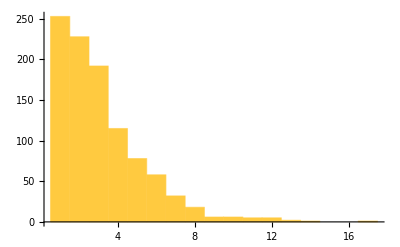

```mathematica
Histogram[Length/@ eps, {1}, PlotRange->All]
```

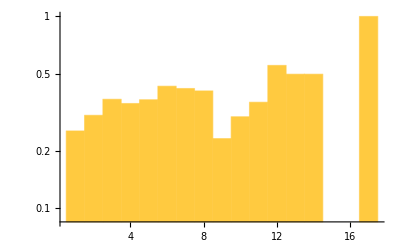

```mathematica
Histogram[Length/@ eps, {1}, "HF", ScalingFunctions->"Log"]
```

#### Finding distribution

```mathematica
FindDistribution[Length/@ eps]
```

MixtureDistribution[{0.737917,0.262083},{BenfordDistribution[5],BinomialDistribution[118,0.0525557]}]